```mathematica
ket0=SparseArray[{{1,1}->1,{2,1}->0}];ket1=SparseArray[{{2,1}->1}];
```

```mathematica
g=Graph[{1->2,1->3,1->4,2->1,2->4,3->4,4->3}]; (*Grafo*)
(*g=Graph[{1->2,1->3,2->4}];*) (*Grafo árbol*)
(*g=Graph[{1->2,1->3,1->4,2->1,3->1,4->1}];*) (*Grafo estrella*)
(*g=Graph[{1->2,2->3,3->1, 1->3,3->2,2->1, 1->4,2->4,3->4}];*) (*Grafo corona*)
g
```

-Graphics-

```mathematica
Em=AdjacencyMatrix[g]; 
For[j=1,j<=4,j++,
	OutDeg=Sum[Em[[j,i]],{i,1,4}];
	If[OutDeg!=0, Em[[j]]=Em[[j]]/OutDeg, Em[[j]]={1/4,1/4,1/4,1/4};]]
Em=Transpose[Em]; (*Matriz de adyacencia del grafo*)
Em//MatrixForm
```

(0 | 1/2 | 0 | 0
1/3 | 0 | 0 | 0
1/3 | 0 | 0 | 1
1/3 | 1/2 | 1 | 0)

```mathematica
G=α Em + (1-α)/(Dimensions[Em][[1]]) Table[1,{Dimensions[Em][[1]]},{Dimensions[Em][[1]]}]; (*Matriz de Google*)
G/.{α->85/100}
```

{{3/80,37/80,3/80,3/80},{77/240,3/80,3/80,3/80},{77/240,3/80,3/80,71/80},{77/240,37/80,71/80,3/80}}

```mathematica
Ivl1={1}; (*PageRank inicial de cada nodo*)
Ivl2={0};
Ivl3={0};
Ivl4={0};
Iv={{1},{0},{0},{0}}; (*Vector de PageRank inicial*)
For[i=1,i≤30,i++,
Iv=(G/.{α->0.85}).Iv; (*Iterar con la matriz de Google*)
(*Iv=Iv/Norm[Iv];*)
AppendTo[Ivl1,Iv[[1,1]]];
AppendTo[Ivl2,Iv[[2,1]]];
AppendTo[Ivl3,Iv[[3,1]]];
AppendTo[Ivl4,Iv[[4,1]]];]
Iv//MatrixForm (*Vector de PageRank final*)
```

(0.0607532
0.0547134
0.435188
0.449345)

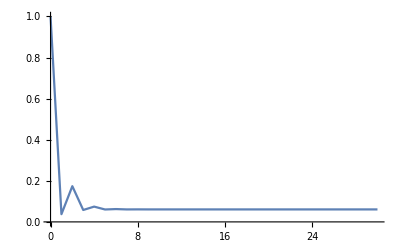

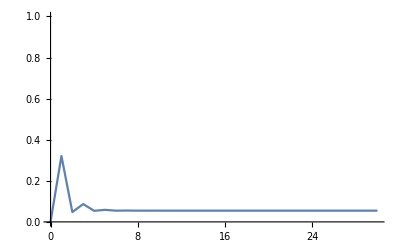

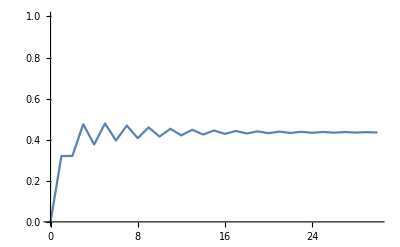

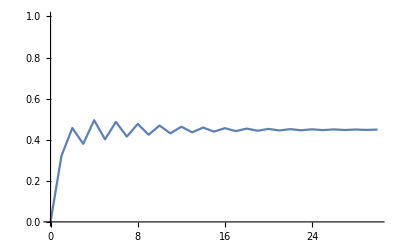

```mathematica
ListLinePlot[Ivl1,PlotRange->{0,1},DataRange->{0,30}] (*Graficar evolución del PageRank de cada nodo*)
ListLinePlot[Ivl2,PlotRange->{0,1},DataRange->{0,30}]
ListLinePlot[Ivl3,PlotRange->{0,1},DataRange->{0,30}]
ListLinePlot[Ivl4,PlotRange->{0,1},DataRange->{0,30}]
```

```mathematica
PageRankCentrality[g,0.85] (*Comparar con el PageRank dado por la función de Mathematica*)
```

{0.0607532,0.0547134,0.435982,0.448551}

```mathematica
ket[k_,n_]:=Table[{i==k},{i,0,n-1}]/.{True->1,False->0}; (*Generador de kets: k -> estado, n -> dimensión*)
```

```mathematica
Subscript[ϕx, j_]:=KroneckerProduct[ket[j-1,4],Sum[√G[[k,j]] ket[k-1,4],{k,1,4}]]; (*Estados A -> B*)
Subscript[ψy, j_]:=KroneckerProduct[Sum[√G[[k,j]] ket[k-1,4],{k,1,4}],ket[j-1,4]]; (*Estados B -> A*)
ϕx0=Sum[Subscript[ϕx, j],{j,1,4}]/2; (*Superposición de los estados A -> B*)
ψy0=Sum[Subscript[ψy, j],{j,1,4}]/2; (*Superposición de los estados B -> A*)
Πx=Sum[Subscript[ϕx, j].Subscript[ϕx, j]†,{j,1,4}]; (*Proyector A -> B*)
Πy=Sum[Subscript[ψy, j].Subscript[ψy, j]†,{j,1,4}]; (*Proyector B -> A*)
S=Sum[KroneckerProduct[ket[j,4],ket[k,4]].KroneckerProduct[ket[k,4],ket[j,4]]†,{j,0,3},{k,0,3}]; (*Operador SWAP*)
Ux=S.(2Πx-IdentityMatrix[16]); (*Operador de difusión 1/2*)
Ax=Sum[Subscript[ϕx, j].ket[j-1,4]†,{j,1,4}]; (*A -> B*)
By=Sum[Subscript[ψy, j].ket[j-1,4]†,{j,1,4}]; (*B -> A*)
H=HadamardMatrix[2]; (*Hadamard*)
s=KroneckerProduct[H,H,H,H].KroneckerProduct[ket[0,2],ket[0,2],ket[0,2],ket[0,2]]//N; (*Estado de superposición uniforme*)
W=(IdentityMatrix[16]-2 Ax.Ax†).(2 s.s†-IdentityMatrix[16]); (*Operador de difusión más Grover-like*)
W=(2 By.By†-IdentityMatrix[16]).(2 Ax.Ax†-IdentityMatrix[16]); (*Operador de difusión 2*)
W=MatrixPower[Ux,2]; (*Operador de difusión 1*)
(*W=MatrixPower[W/.α->0.99,1/10];*)
(*ϕx0=s;*)
```

```mathematica
ϕx0/.α->0.85
```

{{0.0968246},{0.283211},{0.283211},{0.283211},{0.340037},{0.0968246},{0.0968246},{0.340037},{0.0968246},{0.0968246},{0.0968246},{0.471036},{0.0968246},{0.0968246},{0.471036},{0.0968246}}

```mathematica
a=0.85;
qIvl1=Table[((ϕx0†/.{α->a}).MatrixPower[(W†/.{α->a}),m].KroneckerProduct[IdentityMatrix[4],ket[0,4].ket[0,4]†].MatrixPower[(W/.{α->a}),m].(ϕx0/.{α->a}))[[1,1]],{m,1,30}];
qIvl2=Table[((ϕx0†/.{α->a}).MatrixPower[(W†/.{α->a}),m].KroneckerProduct[IdentityMatrix[4],ket[1,4].ket[1,4]†].MatrixPower[(W/.{α->a}),m].(ϕx0/.{α->a}))[[1,1]],{m,1,30}];
qIvl3=Table[((ϕx0†/.{α->a}).MatrixPower[(W†/.{α->a}),m].KroneckerProduct[IdentityMatrix[4],ket[2,4].ket[2,4]†].MatrixPower[(W/.{α->a}),m].(ϕx0/.{α->a}))[[1,1]],{m,1,30}];
qIvl4=Table[((ϕx0†/.{α->a}).MatrixPower[(W†/.{α->a}),m].KroneckerProduct[IdentityMatrix[4],ket[3,4].ket[3,4]†].MatrixPower[(W/.{α->a}),m].(ϕx0/.{α->a}))[[1,1]],{m,1,30}];
```

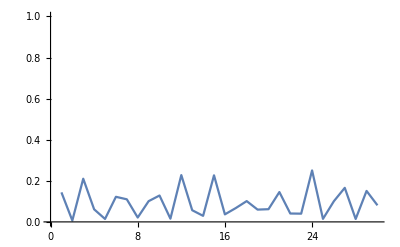

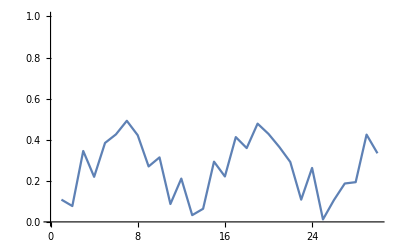

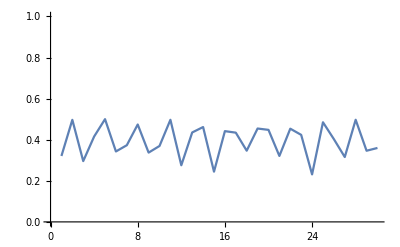

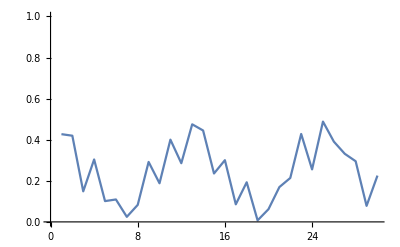

```mathematica
ListLinePlot[qIvl1,PlotRange->{0,1},DataRange->{1,30}]
ListLinePlot[qIvl2,PlotRange->{0,1},DataRange->{1,30}]
ListLinePlot[qIvl3,PlotRange->{0,1},DataRange->{1,30}]
ListLinePlot[qIvl4,PlotRange->{0,1},DataRange->{1,30}]
```

```mathematica
qIvl1
qIvl2
qIvl3
qIvl4
qIvl1//Mean
qIvl2//Mean
qIvl3//Mean
qIvl4//Mean
```

{0.14375,0.00658673,0.210188,0.0612348,0.014347,0.122106,0.109973,0.0212599,0.10087,0.128451,0.0156912,0.227843,0.0568234,0.0294411,0.226719,0.0366675,0.0673459,0.101213,0.0598202,0.0618378,0.145273,0.0408138,0.0401073,0.250626,0.0147594,0.100664,0.165783,0.0142357,0.150729,0.0807447}

{0.108333,0.0771351,0.345166,0.21934,0.38431,0.425899,0.492098,0.421853,0.269953,0.314036,0.0869758,0.210822,0.0328093,0.0638944,0.293143,0.221146,0.412745,0.359302,0.478241,0.428348,0.364228,0.291616,0.10824,0.262662,0.0120697,0.1058,0.18687,0.193382,0.424847,0.333959}

{0.320833,0.496759,0.295936,0.415526,0.500098,0.342826,0.373261,0.4741,0.337312,0.369543,0.496985,0.275679,0.435327,0.461731,0.244478,0.441774,0.434383,0.346627,0.454521,0.447976,0.321021,0.453695,0.423616,0.231171,0.484947,0.402895,0.315823,0.497146,0.346348,0.359921}

{0.427083,0.419519,0.148709,0.3039,0.101244,0.10917,0.0246671,0.0827871,0.291866,0.18797,0.400348,0.285657,0.475041,0.444933,0.235661,0.300412,0.0855263,0.192858,0.0074173,0.0618389,0.169478,0.213876,0.428037,0.255541,0.488223,0.390641,0.331524,0.295237,0.0780756,0.225375}

0.0935302

0.264307

0.393409

0.248754

```mathematica
Dm=Table[√(G[[i,j]] G[[j,i]]),{i,1,4},{j,1,4}];
A=Sum[Subscript[ψ, j].ket[j-1,4]†,{j,1,4}];
```

```mathematica
Eigenvalues[Dm/.{α->0.85}]
Eigenvectors[Dm/.{α->0.85}]
Subscript[λ, i_]:=Table[{Eigenvectors[Dm/.{α->0.85}][[i,j]]},{j,1,4}];
```

{0.991911,-0.856111,0.358113,-0.343913}

{{-0.241118,-0.216451,-0.663401,-0.67447},{0.0388776,-0.0912947,-0.701672,0.705556},{-0.65862,-0.678406,0.255124,0.202229},{0.711738,-0.696117,0.0496684,-0.0798966}}

```mathematica
Subscript[λa, i_]:=A.Subscript[λ, i]/.{α->0.85};
Subscript[λa, 1]
Subscript[λa, 2]
Subscript[λa, 3]
Subscript[λa, 4]
```

{{-0.0466924},{-0.136575},{-0.136575},{-0.136575},{-0.147203},{-0.0419156},{-0.0419156},{-0.147203},{-0.128467},{-0.128467},{-0.128467},{-0.624972},{-0.130611},{-0.130611},{-0.6354},{-0.130611}}

{{0.00752862},{0.0220211},{0.0220211},{0.0220211},{-0.0620871},{-0.0176792},{-0.0176792},{-0.0620871},{-0.135878},{-0.135878},{-0.135878},{-0.661026},{0.13663},{0.13663},{0.664685},{0.13663}}

{{-0.127541},{-0.373056},{-0.373056},{-0.373056},{-0.461366},{-0.131373},{-0.131373},{-0.461366},{0.0494045},{0.0494045},{0.0494045},{0.240345},{0.0391615},{0.0391615},{0.190514},{0.0391615}}

{{0.137827},{0.403144},{0.403144},{0.403144},{-0.473411},{-0.134802},{-0.134802},{-0.473411},{0.00961825},{0.00961825},{0.00961825},{0.0467913},{-0.0154719},{-0.0154719},{-0.0752683},{-0.0154719}}

```mathematica
Eigenvalues[G]/.α->0.85
(Eigenvectors[G][[1]])/Sum[Eigenvectors[G][[1]][[i]],{i,1,4}]/.α->0.85
```

{1,-0.85,-0.347011,0.347011}

{0.0607532,0.0547134,0.435982,0.448551}

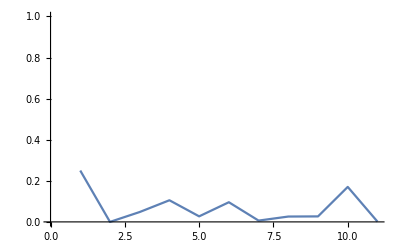

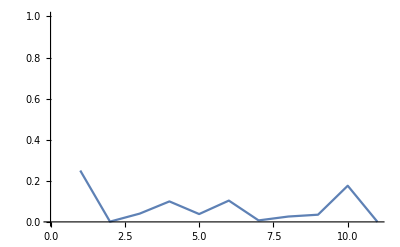

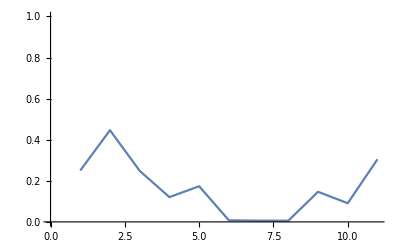

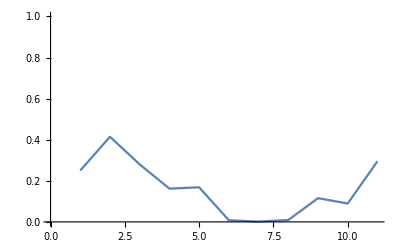

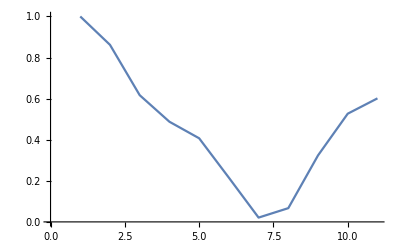

{0.25,6.53607×10^-6,0.0779519,0.215991,0.0663694,0.444453,0.301557,0.389249,0.0826163,0.323255,0.00223396}

{0.25,0.00155875,0.0653528,0.204463,0.0937507,0.481746,0.344988,0.389998,0.108208,0.334197,0.0000757336}

{0.25,0.517717,0.402844,0.247318,0.426189,0.0362799,0.28769,0.0847063,0.452379,0.172645,0.506829}

{0.25,0.480718,0.453852,0.332228,0.41369,0.0375206,0.0657641,0.136046,0.356797,0.169903,0.490861}

{1.,0.861898,0.616787,0.487568,0.407044,0.215312,0.0209348,0.0668965,0.323696,0.526734,0.601324}

```mathematica
qIvl1=Table[Abs[(Subscript[ψ, 1]†.MatrixPower[U/.α->0.85,2m].ψ0/.α->0.85)[[1,1]]]^2,{m,0,10}];
qIvl2=Table[Abs[(Subscript[ψ, 2]†.MatrixPower[U/.α->0.85,2m].ψ0/.α->0.85)[[1,1]]]^2,{m,0,10}];
qIvl3=Table[Abs[(Subscript[ψ, 3]†.MatrixPower[U/.α->0.85,2m].ψ0/.α->0.85)[[1,1]]]^2,{m,0,10}];
qIvl4=Table[Abs[(Subscript[ψ, 4]†.MatrixPower[U/.α->0.85,2m].ψ0/.α->0.85)[[1,1]]]^2,{m,0,10}];
ListLinePlot[qIvl1,PlotRange->{0,1}]
ListLinePlot[qIvl2,PlotRange->{0,1}]
ListLinePlot[qIvl3,PlotRange->{0,1}]
ListLinePlot[qIvl4,PlotRange->{0,1}]
ListLinePlot[qIvl1+qIvl2+qIvl3+qIvl4,PlotRange->{0,1}]
qIvl1/(qIvl1+qIvl2+qIvl3+qIvl4)
qIvl2/(qIvl1+qIvl2+qIvl3+qIvl4)
qIvl3/(qIvl1+qIvl2+qIvl3+qIvl4)
qIvl4/(qIvl1+qIvl2+qIvl3+qIvl4)
qIvl1+qIvl2+qIvl3+qIvl4
```

{{0.868139}}

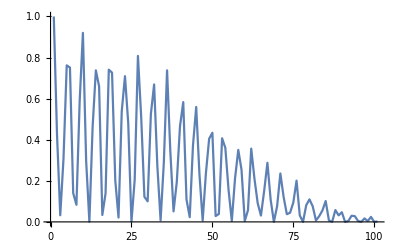

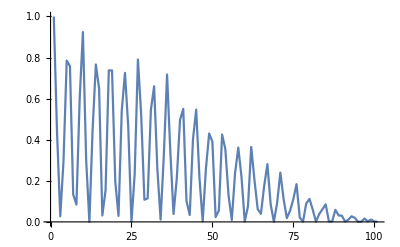

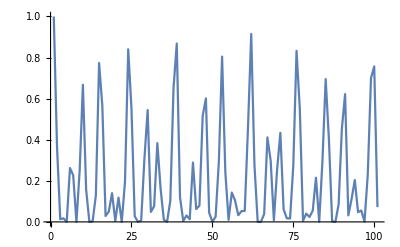

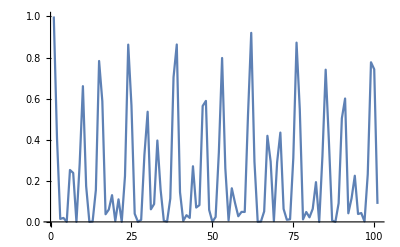

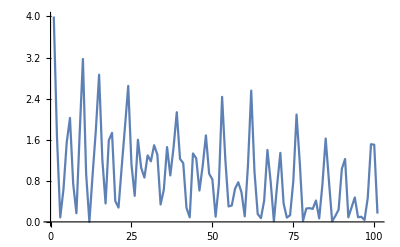

```mathematica
ϕx0†.ψy0/.α->0.85
ListLinePlot[Table[(Abs[(Subscript[ϕx, 1]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 1]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
ListLinePlot[Table[(Abs[(Subscript[ϕx, 2]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 2]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
ListLinePlot[Table[(Abs[(Subscript[ϕx, 3]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 3]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
ListLinePlot[Table[(Abs[(Subscript[ϕx, 4]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 4]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
ListLinePlot[Table[(Abs[(Subscript[ϕx, 1]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 1]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 2]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 2]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 3]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 3]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 4]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 4]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
```

```mathematica
Mean[Table[(Abs[(Subscript[ϕx, 1]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 1]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
Mean[Table[(Abs[(Subscript[ϕx, 2]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 2]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
Mean[Table[(Abs[(Subscript[ϕx, 3]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 3]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
Mean[Table[(Abs[(Subscript[ϕx, 4]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 4]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
Mean[Table[(Abs[(Subscript[ϕx, 1]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 1]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 2]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 2]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 3]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 3]/.α->0.85)]^2)[[1,1]]+(Abs[(Subscript[ϕx, 4]†/.α->0.85).MatrixPower[W/.α->0.85,m].(Subscript[ϕx, 4]/.α->0.85)]^2)[[1,1]],{m,0,100}]]
```

0.228568

0.228913

0.226226

0.23411

0.917817

```mathematica
W//MatrixForm
```

(0.999842 | -0.00929049 | -0.000919442 | -0.000935166 | 0.00837684 | 0.0000645892 | 0.000668354 | 0.00926647 | -0.000901716 | -0.00060013 | 3.6346×10^-6 | -0.000240871 | -0.000884116 | -0.00834981 | 0.000423099 | 5.51118×10^-6
0.00837684 | 0.98417 | 0.0965038 | 0.0963008 | 0.000345886 | -0.00794592 | 0.000147097 | 0.0000402951 | 0.0000536718 | -0.00814195 | -0.0000489303 | -0.00501946 | 0.000217323 | -0.11222 | 0.00228579 | -0.0000882684
-0.000901716 | -0.107041 | 0.989437 | -0.0106996 | 0.0000536718 | -0.00684698 | 0.0000537333 | -0.000246871 | 0.000242618 | -0.0068222 | 0.0000785147 | -0.00115415 | 0.000798844 | -0.0958434 | 0.0126471 | 0.000498301
-0.000884116 | -0.10686 | -0.0103153 | 0.989448 | 0.000217323 | -0.00683692 | 0.000115305 | -0.000139001 | 0.000798844 | -0.00627259 | 0.000679634 | 0.00881715 | 0.000252554 | -0.0964113 | 0.00265685 | -0.00010377
-0.00929049 | -0.000186487 | 0.0000268558 | -0.0000847097 | 0.98417 | 0.00645977 | 0.00666454 | 0.091228 | -0.107041 | -0.00007609 | 0.000128683 | 0.000341057 | -0.10686 | 0.0000966583 | 0.00617673 | 0.000198436
0.0000645892 | 0.00645977 | 0.00759454 | 0.0075851 | -0.00794592 | 0.999842 | -0.0000635298 | -0.0011057 | -0.00684698 | -0.0000919418 | 2.68213×10^-6 | -0.000134726 | -0.00683692 | -0.00112203 | 0.000253999 | 3.30403×10^-6
-0.00060013 | -0.00007609 | -0.000133615 | -0.000091553 | -0.00814195 | -0.0000919418 | 0.99987 | -0.00131246 | -0.0068222 | 3.38474×10^-6 | -0.0000347767 | 0.000145166 | -0.00627259 | 0.000572361 | 0.010258 | 0.000556898
-0.00834981 | 0.0000966583 | 0.000315049 | 0.000147703 | -0.11222 | -0.00112203 | -0.00092799 | 0.984223 | -0.0958434 | 0.000572361 | 0.0007664 | 0.0119361 | -0.0964113 | -0.000019937 | 0.00395416 | 0.0000311074
-0.000919442 | 0.0000268558 | -0.000177457 | -0.00062315 | 0.0965038 | 0.00759454 | 0.00759103 | 0.106484 | 0.989437 | -0.000133615 | -0.000137131 | -0.0116127 | -0.0103153 | 0.000315049 | 0.0022064 | -0.000334956
0.000668354 | 0.00666454 | 0.00759103 | 0.00713872 | 0.000147097 | -0.0000635298 | 3.49936×10^-6 | -0.000422017 | 0.0000537333 | 0.99987 | -0.000063074 | -0.0102689 | 0.000115305 | -0.00092799 | -0.0000299283 | -0.000453808
3.6346×10^-6 | 0.000128683 | -0.000137131 | -0.000537931 | -0.0000489303 | 2.68213×10^-6 | -0.000063074 | -0.000628778 | 0.0000785147 | -0.0000347767 | 0.999899 | -0.00998898 | 0.000679634 | 0.0007664 | 0.0099741 | 0.0000997862
0.000423099 | 0.00617673 | 0.0022064 | -0.00778538 | 0.00228579 | 0.000253999 | -0.0000299283 | -0.010379 | 0.0126471 | 0.010258 | 0.0099741 | 0.999648 | 0.00265685 | 0.00395416 | -0.000322068 | -0.0100079
-0.000935166 | -0.0000847097 | -0.00062315 | -0.000165585 | 0.0963008 | 0.0075851 | 0.00713872 | 0.10692 | -0.0106996 | -0.000091553 | -0.000537931 | -0.00160128 | 0.989448 | 0.000147703 | -0.00778538 | 0.0000668278
0.00926647 | 0.091228 | 0.106484 | 0.10692 | 0.0000402951 | -0.0011057 | -0.000422017 | 0.0000942977 | -0.000246871 | -0.00131246 | -0.000628778 | -0.00384289 | -0.000139001 | 0.984223 | -0.010379 | -0.0000849987
-0.000240871 | 0.000341057 | -0.0116127 | -0.00160128 | -0.00501946 | -0.000134726 | -0.0102689 | -0.00384289 | -0.00115415 | 0.000145166 | -0.00998898 | 0.00044671 | 0.00881715 | 0.0119361 | 0.999648 | 0.00999372
5.51118×10^-6 | 0.000198436 | -0.000334956 | 0.0000668278 | -0.0000882684 | 3.30403×10^-6 | -0.000453808 | -0.0000849987 | 0.000498301 | 0.000556898 | 0.0000997862 | 0.00999372 | -0.00010377 | 0.0000311074 | -0.0100079 | 0.999899)

```mathematica
qIv1=((ϕx0†).(W†).KroneckerProduct[IdentityMatrix[4],ket[0,4].ket[0,4]†].(W).(ϕx0))[[1,1]];
qIv2=((ϕx0†).(W†).KroneckerProduct[IdentityMatrix[4],ket[1,4].ket[1,4]†].(W).(ϕx0))[[1,1]];
qIv3=((ϕx0†).(W†).KroneckerProduct[IdentityMatrix[4],ket[2,4].ket[2,4]†].(W).(ϕx0))[[1,1]];
qIv4=((ϕx0†).(W†).KroneckerProduct[IdentityMatrix[4],ket[3,4].ket[3,4]†].(W).(ϕx0))[[1,1]];
qIv1/.α->0.85
qIv2/.α->0.85
qIv3/.α->0.85
qIv4/.α->0.85
```

0.14375

0.108333

0.320833

0.427083

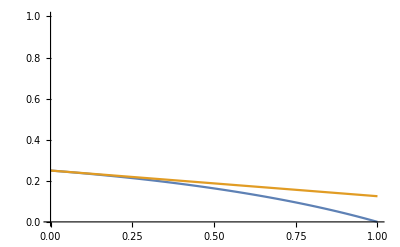

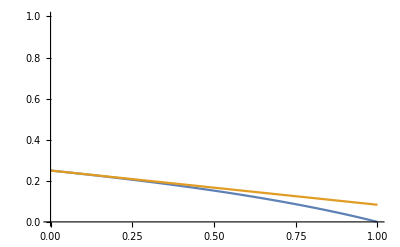

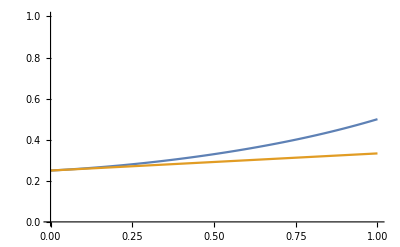

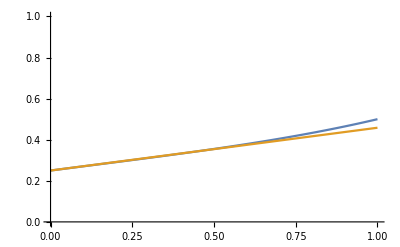

```mathematica
Plot[{PageRankCentrality[g,α][[1]],qIv1},{α,0,1},PlotRange->{0,1}]
Plot[{PageRankCentrality[g,α][[2]],qIv2},{α,0,1},PlotRange->{0,1}]
Plot[{PageRankCentrality[g,α][[3]],qIv3},{α,0,1},PlotRange->{0,1}]
Plot[{PageRankCentrality[g,α][[4]],qIv4},{α,0,1},PlotRange->{0,1}]
```

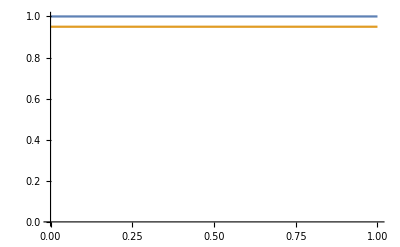

-Graphics-

-Graphics-

```mathematica
Plot[{(PageRankCentrality[g,α][[1]]>PageRankCentrality[g,α][[2]])/.{True->1,False->0.03},(qIv1>qIv2)/.{True->0.95,False->0.015}},{α,0,1},PlotRange->{0,1}]
Plot[{(PageRankCentrality[g,α][[3]]>PageRankCentrality[g,α][[1]])/.{True->1,False->0.03},(qIv3>qIv1)/.{True->0.95,False->0.015}},{α,0,1},PlotRange->{0,1}]
Plot[{(PageRankCentrality[g,α][[4]]>PageRankCentrality[g,α][[3]])/.{True->1,False->0.03},(qIv4>qIv3)/.{True->0.95,False->0.015}},{α,0,1},PlotRange->{0,1}]
```

```mathematica
FindMinimum[{qIv1,0≤α≤1},α]
FindMinimum[{qIv2,0≤α≤1},α]
FindMaximum[{qIv3,0≤α≤1},α]
FindMaximum[{qIv4,0≤α≤1},α]
```

{0.125529,{α→0.676456}}

{0.0833666,{α→0.673727}}

{0.333462,{α→0.653095}}

{0.457873,{α→0.684211}}

```mathematica
FindMinimum[{qIv1,0≤α≤1},α]
FindMinimum[{qIv2,0≤α≤1},α]
FindMaximum[{qIv3,0≤α≤1},α]
FindMaximum[{qIv4,0≤α≤1},α]
```

{0.125,{α→0.999996}}

{0.0833338,{α→0.999997}}

{0.333333,{α→0.999995}}

{0.458333,{α→0.999998}}